### PARAMETRES

```mathematica
ClearAll;
```

```mathematica
listH ={100,500,500}; (*мощности слоев*)
slopes = {0Degree, -0.9 Degree, -0.3 Degree, 2 Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

type = 1 ;
listV = {1500,2000,2300,2500, 2800}; (*набор скоростей *)
```

```mathematica
(*folding parametres *)
hDispersion = 300;(*степень складчатости нижнего слоя в метрах*)
hTapering =2; (*степень влияния нижнего горизонта на верхние*)
gaussRadius = 5; (*start filter radius for GaussianFilter*)
```

```mathematica
velocityTrend = {0,1,1,1,1};(*1 or 0*)
velocityAnomaly ={1,0,0,0,0}; (*1 or 0*)
```

```mathematica
wellCount= 10 ;(*кол скважин*)
wellType = "random"; (*расположение скважин "max","min","regular","random"*)
```

### DEPTH

```mathematica
horizons = BuildDepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["horizons"]];
table = BuildDepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["table"]];
optsDepth = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"};
PlotDepthSection[horizons, optsDepth]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]];
datasetVelModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]]
```

Dataset[<>]

```mathematica
(*PlotVelocity[velModel, horizons]*)
```

### TIME

```mathematica
time=BuildTimeSection[horizons, velModel][["time"]];
optsTime = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section"};
PlotTimeSection[time, optsTime]
```

-Graphics-

### WELLS

```mathematica
wellDataset = BuildWellSet[horizons, time, wellCount, wellType][["dataset"]];
positions = BuildWellSet[horizons, time,  wellCount, wellType][["positions"]];
PlotDepthSection[horizons, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section",GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},											
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

### HTMethod

{FittedModel[3.78641+2612.99 t],FittedModel[-50.6986+4367.34 t],FittedModel[-6.7987+4181.46 t],FittedModel[415.936+3044.68 t]}

{{{0.00779997,23.6803},{0.00785036,23.6803},{0.00875134,25.6803},{0.0174877,50.6803},{0.023815,71.6803},{0.0265418,71.6803},{0.0251654,72.6803},{0.0247082,72.6803},{0.0252554,68.6803},{0.0266318,63.6803}},{{0.0701085,265.68},{0.0679505,256.68},{0.0601531,222.68},{0.06423,232.68},{0.0834687,301.68},{0.0546536,182.68},{0.0702918,250.68},{0.0746394,272.68},{0.0548463,185.68},{0.0354658,98.6803}},{{0.200668,830.68},{0.198504,816.68},{0.187013,751.68},{0.196333,804.68},{0.209834,846.68},{0.191213,794.68},{0.205911,859.68},{0.216795,927.68},{0.189881,801.68},{0.170336,720.68}},{{0.379888,1582.68},{0.36752,1537.68},{0.326927,1379.68},{0.374429,1558.68},{0.386463,1586.68},{0.410366,1678.68},{0.43496,1751.68},{0.507117,1927.68},{0.436527,1758.68},{0.42465,1724.68}}}

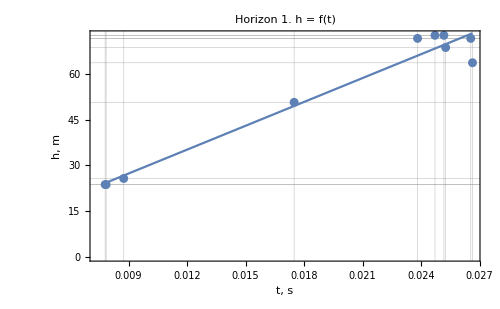
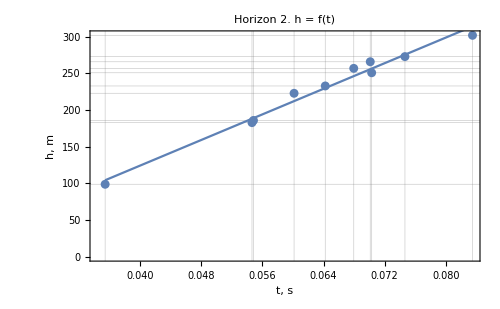
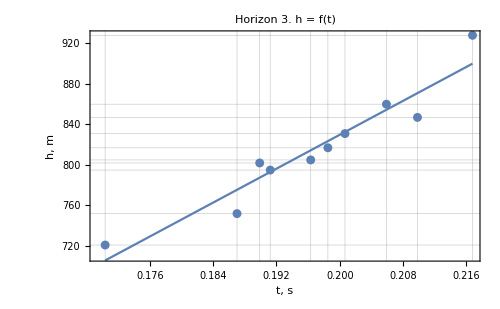
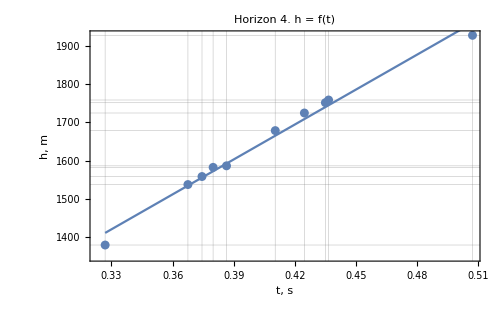

```mathematica
Clear[t];
lmSetHT=HTMethod[wellDataset,time, t][["lmSet"]]
lmParametresHT=HTMethod[wellDataset, time, t][["lmParametres"]];
resultHT=HTMethod[wellDataset, time, t][["result"]];
wellValuesHT=HTMethod[wellDataset, time, t][["wellValues"]]
PlotHT[wellValuesHT,lmSetHT, t]
```

### VTMethod

{FittedModel[3136.73-14595.8 t],FittedModel[2339.46+18623.8 t],FittedModel[4168.32-108.546 t],FittedModel[5035.1-2347.05 t]}

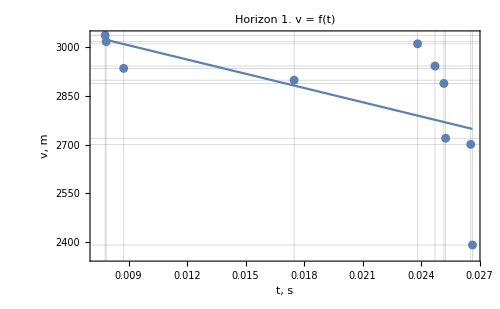
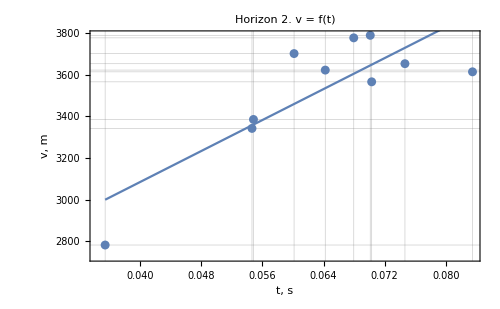
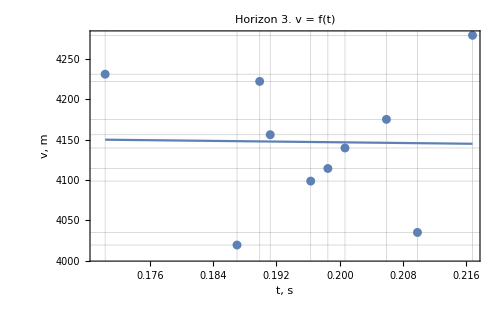
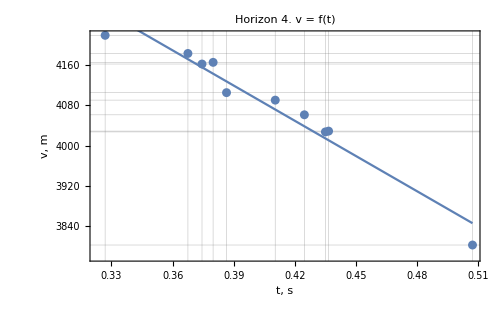

```mathematica
lmSetVT=VTMethod[wellDataset,time, t][["lmSet"]]
lmParametresVT=VTMethod[wellDataset,time, t][["lmParametres"]];
wellValuesVT=VTMethod[wellDataset,time, t][["wellValues"]];
resultVT = VTMethod[wellDataset, time, t][["result"]];
fitsVT = VTMethod[wellDataset, time, t][["fits"]];
PlotVT[wellValuesVT,lmSetVT, t]
```

### THMethod

{FittedModel[-0.00066491+0.000368309 h],FittedModel[0.0126098+0.000224561 h],FittedModel[0.018249+0.000218767 h],FittedModel[-0.128967+0.000323805 h]}

{{{23.6803,0.00779997},{23.6803,0.00785036},{25.6803,0.00875134},{50.6803,0.0174877},{71.6803,0.023815},{71.6803,0.0265418},{72.6803,0.0251654},{72.6803,0.0247082},{68.6803,0.0252554},{63.6803,0.0266318}},{{265.68,0.0701085},{256.68,0.0679505},{222.68,0.0601531},{232.68,0.06423},{301.68,0.0834687},{182.68,0.0546536},{250.68,0.0702918},{272.68,0.0746394},{185.68,0.0548463},{98.6803,0.0354658}},{{830.68,0.200668},{816.68,0.198504},{751.68,0.187013},{804.68,0.196333},{846.68,0.209834},{794.68,0.191213},{859.68,0.205911},{927.68,0.216795},{801.68,0.189881},{720.68,0.170336}},{{1582.68,0.379888},{1537.68,0.36752},{1379.68,0.326927},{1558.68,0.374429},{1586.68,0.386463},{1678.68,0.410366},{1751.68,0.43496},{1927.68,0.507117},{1758.68,0.436527},{1724.68,0.42465}}}

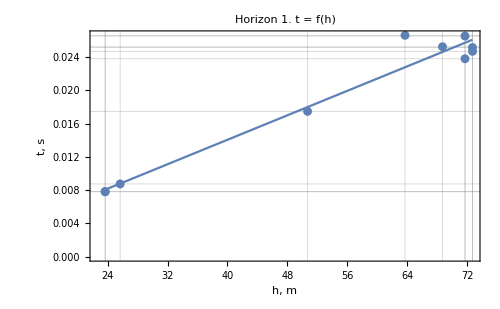
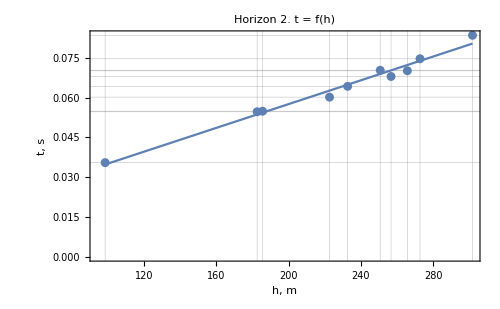
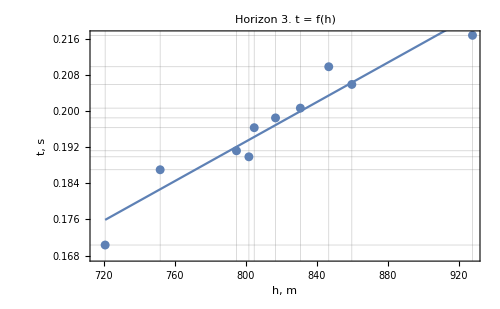
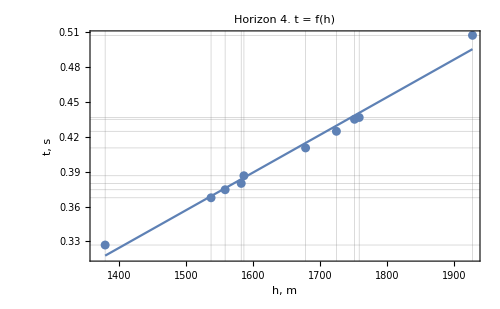

```mathematica
Clear[h];
lmSetTH=THMethod[wellDataset,time, h][["lmSet"]]
lmParametresTH=THMethod[wellDataset, time, h][["lmParametres"]];
wellValuesTH = THMethod[wellDataset, time, h][["wellValues"]]
resultTH=THMethod[wellDataset, time, h][["result"]];
PlotTH[wellValuesTH,lmSetTH, h]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod[wellDataset,time][["vAveTable"]]
resultVave=VaveMethod[wellDataset, time][["result"]];
fitsVave = VaveMethod[wellDataset, time][["fits"]];
```

{2853.57,3523.58,4146.97,4084.81}

### VaveVOGTMethod

{FittedModel[1.19392×10^-11+0.844222 v],FittedModel[4.53353×10^-11+0.804094 v],FittedModel[-1.15043×10^-12+1.0406 v],FittedModel[-1.96147×10^-10+1.91692 v]}

{{3.28453×10^-11,0.974735},{4.58715×10^-11,1.07734},{-8.3308×10^-10,1.92261},{-4.00395×10^-11,1.06052}}

{{{23.6803},{23.6803},{25.6803},{50.6803},{71.6803},{71.6803},{72.6803},{72.6803},{68.6803},{63.6803}},{{265.68},{256.68},{222.68},{232.68},{301.68},{182.68},{250.68},{272.68},{185.68},{98.6803}},{{830.68},{816.68},{751.68},{804.68},{846.68},{794.68},{859.68},{927.68},{801.68},{720.68}},{{1582.68},{1537.68},{1379.68},{1558.68},{1586.68},{1678.68},{1751.68},{1927.68},{1758.68},{1724.68}}}

{{{300,0.},{400,0.},{800,0.},{2000,0.},{2800,0.},{5200,0.},{6600,0.},{7400,0.},{8000,0.},{8800,0.}},{{0,-24.729},{100,-24.4343},{200,-23.7823},{300,-23.6803},{400,-23.6803},{500,-23.7862},{600,-24.0017},{700,-24.7823},{800,-25.6803},{900,-26.6993},{1000,-27.8433},{1100,-29.5674},{1200,-31.418},{1300,-33.3834},{1400,-35.4514},{1500,-37.6097},{1600,-39.8461},{1700,-42.5998},{1800,-44.9553},{1900,-47.8037},{2000,-50.6803},{2100,-53.1196},{2200,-56.0109},{2300,-58.8886},{2400,-61.7388},{2500,-64.0956},{2600,-66.8486},{2700,-69.0804},{2800,-71.6803},{2900,-73.731},{3000,-75.2186},{3100,-77.0324},{3200,-78.2551},{3300,-79.3243},{3400,-80.2275},{3500,-80.969},{3600,-81.1121},{3700,-81.1237},{3800,-81.019},{3900,-80.8132},{4000,-80.0699},{4100,-79.7076},{4200,-78.8382},{4300,-77.9285},{4400,-76.9938},{4500,-76.501},{4600,-75.562},{4700,-74.6435},{4800,-73.7609},{4900,-73.3809},{5000,-72.6083},{5100,-72.3437},{5200,-71.6803},{5300,-71.5177},{5400,-71.4006},{5500,-71.3254},{5600,-71.2887},{5700,-71.2866},{5800,-71.3156},{5900,-71.3722},{6000,-71.4527},{6100,-71.5534},{6200,-71.6709},{6300,-72.2531},{6400,-72.3931},{6500,-72.5381},{6600,-72.6803},{6700,-72.8111},{6800,-73.3734},{6900,-73.4553},{7000,-73.4999},{7100,-73.4983},{7200,-73.4421},{7300,-73.3226},{7400,-72.6803},{7500,-72.422},{7600,-71.655},{7700,-71.2931},{7800,-70.4438},{7900,-69.5693},{8000,-68.6803},{8100,-67.7875},{8200,-66.9015},{8300,-66.0329},{8400,-65.6442},{8500,-64.8426},{8600,-64.0904},{8700,-63.85},{8800,-63.6803},{8900,-63.592},{9000,-63.5959},{9100,-63.7024},{9200,-64.374},{9300,-64.718},{9400,-65.6483},{9500,-66.7239},{9600,-67.9556},{9700,-69.354},{9800,-71.3813},{9900,-73.145},{10000,-75.5589}},{{0,-289.017},{100,-282.195},{200,-274.111},{300,-265.68},{400,-256.68},{500,-247.269},{600,-238.36},{700,-230.111},{800,-222.68},{900,-216.224},{1000,-211.278},{1100,-207.999},{1200,-206.465},{1300,-206.641},{1400,-207.719},{1500,-210.03},{1600,-213.147},{1700,-217.401},{1800,-221.986},{1900,-226.853},{2000,-232.68},{2100,-238.962},{2200,-245.946},{2300,-253.5},{2400,-261.873},{2500,-270.933},{2600,-280.549},{2700,-290.968},{2800,-301.68},{2900,-312.176},{3000,-321.946},{3100,-330.479},{3200,-337.266},{3300,-341.418},{3400,-342.439},{3500,-340.367},{3600,-334.964},{3700,-326.75},{3800,-315.867},{3900,-302.836},{4000,-288.176},{4100,-273.166},{4200,-257.568},{4300,-243.039},{4400,-229.722},{4500,-217.757},{4600,-207.664},{4700,-199.208},{4800,-192.908},{4900,-188.147},{5000,-185.38},{5100,-183.443},{5200,-182.68},{5300,-182.299},{5400,-183.023},{5500,-184.057},{5600,-186.125},{5700,-188.435},{5800,-191.707},{5900,-195.908},{6000,-201.003},{6100,-206.955},{6200,-214.109},{6300,-222.429},{6400,-231.123},{6500,-240.872},{6600,-250.68},{6700,-260.267},{6800,-268.594},{6900,-275.762},{7000,-280.731},{7100,-283.222},{7200,-282.956},{7300,-279.651},{7400,-272.68},{7500,-262.538},{7600,-249.954},{7700,-235.659},{7800,-219.63},{7900,-202.6},{8000,-185.68},{8100,-168.846},{8200,-152.83},{8300,-138.366},{8400,-125.049},{8500,-114.372},{8600,-105.929},{8700,-100.833},{8800,-98.6803},{8900,-100.583},{9000,-106.516},{9100,-117.212},{9200,-132.647},{9300,-153.554},{9400,-179.908},{9500,-211.685},{9600,-249.617},{9700,-293.68},{9800,-343.471},{9900,-399.722},{10000,-462.03}},{{0,-846.687},{100,-846.12},{200,-840.438},{300,-830.68},{400,-816.68},{500,-800.079},{600,-782.518},{700,-765.637},{800,-751.68},{900,-741.686},{1000,-735.489},{1100,-735.326},{1200,-739.537},{1300,-747.223},{1400,-757.446},{1500,-768.667},{1600,-779.347},{1700,-788.548},{1800,-796.539},{1900,-801.781},{2000,-804.68},{2100,-806.456},{2200,-807.138},{2300,-807.964},{2400,-810.171},{2500,-814.391},{2600,-821.259},{2700,-832.012},{2800,-846.68},{2900,-864.694},{3000,-884.88},{3100,-906.666},{3200,-927.073},{3300,-944.928},{3400,-957.248},{3500,-962.239},{3600,-959.301},{3700,-947.231},{3800,-927.836},{3900,-902.325},{4000,-873.107},{4100,-843.799},{4200,-817.416},{4300,-796.366},{4400,-781.256},{4500,-773.292},{4600,-771.269},{4700,-773.986},{4800,-779.636},{4900,-785.812},{5000,-790.734},{5100,-793.265},{5200,-794.68},{5300,-793.845},{5400,-792.035},{5500,-789.923},{5600,-788.181},{5700,-787.484},{5800,-787.298},{5900,-788.9},{6000,-791.757},{6100,-796.543},{6200,-803.327},{6300,-812.784},{6400,-825.585},{6500,-841.121},{6600,-859.68},{6700,-879.664},{6800,-899.474},{6900,-917.514},{7000,-931.583},{7100,-940.083},{7200,-942.621},{7300,-938.202},{7400,-927.68},{7500,-911.185},{7600,-890.967},{7700,-868.677},{7800,-845.365},{7900,-823.285},{8000,-801.68},{8100,-782.805},{8200,-765.298},{8300,-750.21},{8400,-737.989},{8500,-728.477},{8600,-722.124},{8700,-719.376},{8800,-720.68},{8900,-727.086},{9000,-738.439},{9100,-756.993},{9200,-781.99},{9300,-816.287},{9400,-858.524},{9500,-910.956},{9600,-973.428},{9700,-1045.18},{9800,-1126.06},{9900,-1215.91},{10000,-1312.77}},{{0,-1500.19},{100,-1557.56},{200,-1592.31},{300,-1582.68},{400,-1537.68},{500,-1481.29},{600,-1426.92},{700,-1397.67},{800,-1379.68},{900,-1381.1},{1000,-1388.96},{1100,-1411.38},{1200,-1429.94},{1300,-1451.42},{1400,-1475.52},{1500,-1501.1},{1600,-1520.83},{1700,-1537.07},{1800,-1543.38},{1900,-1551.81},{2000,-1558.68},{2100,-1565.81},{2200,-1553.91},{2300,-1537.14},{2400,-1519.95},{2500,-1514.75},{2600,-1522.48},{2700,-1544.96},{2800,-1586.68},{2900,-1617.79},{3000,-1647.16},{3100,-1688.07},{3200,-1734.41},{3300,-1796.82},{3400,-1852.5},{3500,-1900.56},{3600,-1922.49},{3700,-1901.52},{3800,-1847.29},{3900,-1767.67},{4000,-1690.76},{4100,-1620.92},{4200,-1558.97},{4300,-1518.07},{4400,-1501.69},{4500,-1513.31},{4600,-1540.56},{4700,-1578.12},{4800,-1632.1},{4900,-1676.07},{5000,-1702.99},{5100,-1701.49},{5200,-1678.68},{5300,-1661.91},{5400,-1645.09},{5500,-1639.72},{5600,-1639.74},{5700,-1661.92},{5800,-1681.7},{5900,-1692.13},{6000,-1700.31},{6100,-1686.97},{6200,-1682.96},{6300,-1678.69},{6400,-1683.02},{6500,-1710.93},{6600,-1751.68},{6700,-1798.},{6800,-1845.26},{6900,-1890.57},{7000,-1916.12},{7100,-1931.34},{7200,-1950.08},{7300,-1945.7},{7400,-1927.68},{7500,-1890.8},{7600,-1844.11},{7700,-1799.3},{7800,-1777.73},{7900,-1758.53},{8000,-1758.68},{8100,-1760.83},{8200,-1762.6},{8300,-1749.28},{8400,-1731.68},{8500,-1712.69},{8600,-1704.},{8700,-1710.26},{8800,-1724.68},{8900,-1736.96},{9000,-1746.46},{9100,-1758.73},{9200,-1766.09},{9300,-1788.15},{9400,-1813.72},{9500,-1854.49},{9600,-1907.2},{9700,-1974.73},{9800,-2065.26},{9900,-2169.35},{10000,-2289.9}}}

{{{1227.65,1526.48},{1220.81,1517.97},{1187.57,1476.64},{1165.36,1449.03},{1198.65,1490.43},{1082.13,1345.53},{1150.11,1430.07},{1189.44,1478.96},{1111.6,1382.18},{972.547,1209.28}},{{1386.7,1897.88},{1384.43,1894.78},{1359.39,1860.51},{1329.53,1819.64},{1313.3,1797.42},{1213.64,1661.03},{1289.94,1765.45},{1340.32,1834.4},{1258.25,1722.08},{1039.95,1423.3}},{{2379.46,2067.78},{2381.78,2069.79},{2316.84,2013.36},{2360.44,2051.25},{2310.53,2007.88},{2400.51,2086.07},{2388.92,2076.},{2465.58,2142.62},{2421.15,2104.},{2430.33,2111.98}},{{2123.71,2080.04},{2126.82,2083.09},{2151.56,2107.32},{2127.81,2084.06},{2107.1,2063.78},{2078.33,2035.6},{2073.04,2030.41},{1918.68,1879.23},{2058.72,2016.39},{2079.37,2036.62}}}

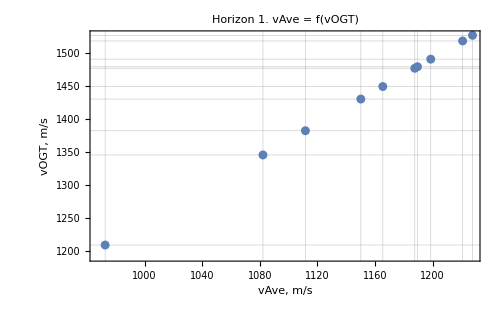
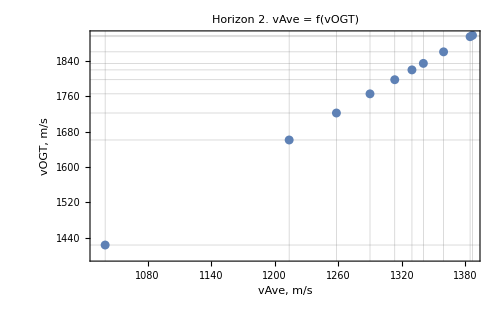
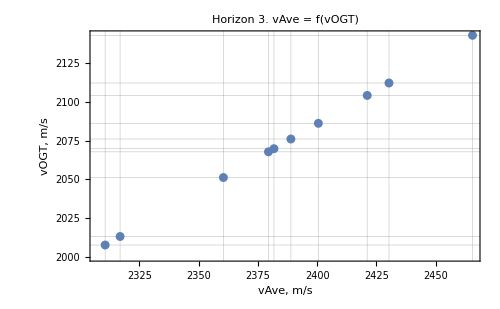
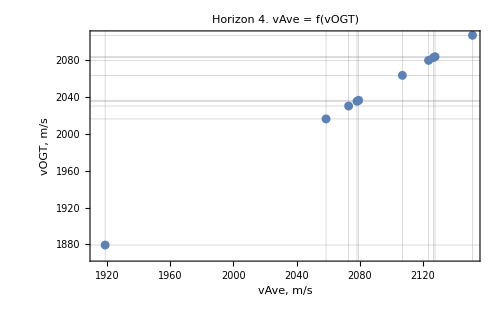

```mathematica
Clear[v];
lmSetVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["lmSet"]]
lmParametresVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["lmParametres"]]
wellValuesVaveVOGT= VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["wellValues"]]
resultVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["result"]]
plotDataVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["plotData"]]
PlotVaveVOGT[plotDataVaveVOGT,lmSetVaveVOGT, v]
```

### GRAPHICS

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1600,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->{Blue}],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->{Orange}],
	ListLinePlot[resultTH[[2;;-1]], PlotStyle->{Green}],
ListLinePlot[resultVave[[2;;-1]], PlotStyle->{Red}],
ListLinePlot[resultVaveVOGT[[2;;-1]], PlotStyle->{Yellow}]
]
```

-Graphics-

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVaveVOGT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "VaveVOGT"]
-Graphics-
```